## Sound Production

```mathematica
(* play a note immediately *)
gme[n_]:=EmitSound[Sound[SoundNote[n,2,"ElectricBass"]]];
Row@Table[
Module[{note=n},
Button[note,gme[note],Method->"Preemptive"]],
{n,Range[0,12]}]
```

0123456789101112

```mathematica
gme[0]
```

### Setup

```mathematica
On[Assert];
```

### Removed Code

#### ToPitch

(*
toPitch/:toPitch[a_,key_:"major"]+i_Integer:=toPitch[a+i,key];
*)
(*
toPitch[str_String,key_:"major"]:=toPitch[ToLowerCase[str],key];
toPitch[-str_String,key_:"major"]:=toPitch[str,key]-12;
toPitch[a_Integer+b_String,key_:"major"]:=12a+toPitch[b,key];
*)

### Function Transformations, Utilities

snd represents a sound function object

```mathematica
heads=(s|p|note|n|freq);
ClearAll[rescale];
rescale[c_][(h:heads)[snd_,t_]]:=h[snd,c t];

ClearAll[reassign];
reassign[u_][(h:heads)[snd_,t_,o___]]:=h[snd,u,o];

ClearAll[getTime];
getTime[(h:heads)[snd_,t_]]:=t;
```

toObject
	parse syntax input into function-y representation.
toSound
	All sound prititives must implement this.
	This converts structured functions into Sound objects
getTime
	All sound primitives must implement this.
	s, p, note, n already defined.

### Syntax (valid input syntax)

Syntax consists of objects.
Objects include:
	all primitives entered explicitly (via function code in syntax)
		s[{__}, t]
		f[frList, t]
	primitives which combine objects
		s, p
	lists of objects
	Integers
	strings like "do", "re", "mi" etc.
	objects with subscripts
	* Consider adding things from the Music` package.

### Syntax Parsing

Do tasks one thing at a time
	know when transformations happen.

Look at everything supplied
	nothing should auto-evaluate unless transformed
	unless for good reason (explicit functions)
convert syntax to appropriate objects
	Map a transformation function over the supplied objects
	define rules to convert to objects
Make the timing work

#### toObject

```mathematica
ClearAll[toObject];
toObject[obj_]:=obj; (* base case, leaves* of tree. *)
(* Subscripts *)
toObject[Subscript[obj_,dur_?NumberQ]]:=reassign[dur][toObject[obj]];
(* Rests *)
toObject[r]:=note[None];
```

### Classes of Sound functions

#### Sequence s of sounds

```mathematica
ClearAll[s];
toObject[s[snd_List,dur_:1]]:=s[toObject/@snd,dur];
toObject[snd_List]:=s[toObject/@snd,1];

s[{obj_},dur_]:=reassign[dur][obj];
s/:toSound[s[snd:{(_:heads)[__]..} ,dur_]]:=Sound[toSound/@snd,dur];
```

```mathematica
ClearAll[sflatten];
sflatten[s[snd_List,dur_]]:=rescale[dur/Norm[getTime/@snd]]/@snd;
```

#### List p of sounds to play in parallel

must normalize time duration of components, so they are equal.
	this might not matter
	Maybe just default to align start times, and call yourself done when the longest inner function finishes.

Probably will implement by giving Sound functions with time specs which make them simultaneous. These _Sound objects will be assembled into a list and that list should be eventually passed to an outer Sound function.
• Dont convert to Sound object until needed, so you can manipulate time values later.
• Note that time specs can be Scaled.

Evaluation & Simplification
p of a single object should be just that object
Find a way to simplify the case for when the arguments to p are all note objects.
	these should be refactored to note objects.

```mathematica
ClearAll[p];
p/:toObject[p[snd_List,t_:1]]:=p[toObject/@snd,t];
p[{obj_},t_]:=reassign[t][obj];

(* This is current best guess for parallelization *)
p/:toSound[p[snd:{(_:heads)[__]..},dur_]]:=Sound[
Sound[toSound[#],{0}]&/@snd,dur]
```

This works: 
sound[{
sound[{sound[SoundNote[4],1],sound[SoundNote[2],1],sound[SoundNote[0],2]},{0,1}],
sound[{sound[SoundNote[7],1],sound[SoundNote[5],1],sound[SoundNote[4],2]},{0,1}]},2]/.sound→Sound

p[{
	s[{n[4,1],n[2,1],n[0,2]},1],
	s[{n[7,1],n[5,1],n[4,2]},1]
},1]

Example code for correct simultaneous playback:
	Sound[{
SoundNote[0,1,"Xylophone"],
Sound[{
Play[.2Sin[2 π 440 t],{t,0,1}],
SoundNote[-1,.1,"Marimba"],
SoundNote[0,{0,1}],
SoundNote[7,{0,1}]},
3],
SoundNote[12,1,"Xylophone"]},
5]
Sound containing sequence of things to play
	SoundNotes can have specification {0,1} to fill whole of outer space.

#### List freq of weighted frequencies

can take a single frequency, list of frequencies, or a list of 2 lists containing the amplitudes and frequencies to be played, respectively.

```mathematica
ClearAll[freq];
toObject[f[fr_,t_:1]]:=freq[fr,t];

(* Single frequency *)
toSound[freq[f_,tmax_:1]]^:=play[
env[tmax][t]Sin[2π f t],
{t,0,tmax}];
(* List of frequencies, equal amplitudes *)
toSound[freq[f_?VectorQ,tmax_:1]]^:=play[
env[tmax][t]Total[Sin[2π f t]],
{t,0,tmax}];
(* Weighted frequencies *)
toSound[freq[f_?MatrixQ,tmax_:1]]^:=play[
env[tmax][t]f⟦1⟧.Sin[2π f⟦2⟧t],
{t,0,tmax}];
```

#### Note n, as a note in a scale

2 cases:
	base scale, (usually major)
	arbitrary chromatic note.
	- Maybe also accidentals.
	> these are all syntax things
	> should be transformed at function level, not syntax level.

Need a converter to frequencies OR to SoundNotes - depending on how its used.

Make a way to change key in syntax.
Ok this is global.
	Now make a better one which does things locally and uses function stuff to carry info around.
	The current version might not even work unless you do this, because of evaluation order.
	nKey="major";
toObject[n["key"→new_]]:=(nKey=new;Nothing);
	Not sure whether this should happen at Syntax or Object level.

Choosing form for notes: SoundNotes or Frequencies
	for SoundNotes, use the note function
	for frequencies, need a converter from pitches to frequencies.

```mathematica
ClearAll[n];
(* Syntax Handling: interpreting syntax as notes in chromatic scale *)
toObject[i_Integer]:=n[toPitch[i](* !!! Use Options here to add support for Keys *)];
toObject[(noteString_String)?(StringMatchQ[solfegg])]:=n[toPitch[noteString]];
toObject[-(noteString_String)?(StringMatchQ[solfegg])]:=n[toPitch[-noteString]];
toObject[α_Integer+(noteString_String)?(StringMatchQ[solfegg])]:=n[12α+toPitch[noteString]]
(*toObject[Subscript[obj_n,key:scaleTypes]]:=reKey[key][toObject[obj,"Key"->key]];*)
```

```mathematica
(* Convert to note head - soundnote container *)
n[pitch_Integer,t_:1]:=note[pitch,t];
n[s_String]:=n[toPitch[s]];
n[-s_String]:=n[toPitch[s]];
n[α_Integer+s_String]:=n[12α+toPitch[s]];
```

Dependencies for n:

```mathematica
solfegg=Union[
{"do","di","re","ri","mi","fa",
"fi","so","si","la","li","ti"},
{"do","ra","re","me","mi","fa",
"se","so","le","la","te","ti"}];
scaleTypes=("major"|"minor");

ClearAll[toPitch];
toPitch[stuff_]:=toPitch[stuff,"major"];

Thread[Evaluate[toPitch[#,"major"]&/@
{1,2,3,4,5,6,7,8}]=
{0,2,4,5,7,9,11,12}];
Thread[Evaluate[toPitch[#,"minor"]&/@
{1,2,3,4,5,6,7,8}]=
{0,2,3,5,7,8,10,12}];
Thread[Evaluate[toPitch[#,key_:"NA"]&/@
{"do","di","re","ri","mi","fa",
"fi","so","si","la","li","ti"}]=
Range[0,11]];
Thread[Evaluate[toPitch[#,key_:"NA"]&/@
{"do","ra","re","me","mi","fa",
"se","so","le","la","te","ti"}]=
Range[0,11]];//Quiet

toPitch[x_Integer,key:scaleTypes]:=12*⌊(x-1)/7⌋+toPitch[Mod[x,7,1],key];
```

#### note wrapper for SoundNote expressions

ARGS
when pitch is a single object, that object is played
	integer number of half steps from middle C
	string representing letter note name and sharp/flat
	None - a rest
	string representing precussion event
when pitch is a list, objects are played in parallel

Sound for a chord: Sound[{SoundNote["C",{0,0.3}],SoundNote["G",{0.1,0.5}]}]
Alternative: Sound[SoundNote[{"C","G"}]]
To preserve this syntax I might want to represent times in terms of beats (actually theyd have to be local beats for measure - but dont have measures) and convert to time later.
	I'd like to specify the time intervals by beats in the current scope.

Sound[]
	Convert these to Sound objects using just the Sound function.
	They can be provided in a list

```mathematica
ClearAll[note,defaultInstrument];
(* Instrument setup *)
(*defaultInstrument:="Piano";*)
Options[note]:={"Instrument":>defaultInstrument};

(* Conversion to Objects *)
toObject[(instr_String)[p_,t_:1]]:=note[p,t,instr];
toObject[(precussion_String)?(!StringMatchQ[#,solfegg]&)]:=note[precussion,1];
(* Interpretation when Instruments are specified *)
toObject[(instr_String)[obj_]]:=
Block[{defaultInstrument=instr},toObject[obj]]
toObject[obj_,"Instrument"->instr_]:=
Block[{defaultInstrument=instr},toObject[obj]];

(* Evaluation *)
note[pitch_,t_:1,OptionsPattern[]]:=note[pitch,t,ℐ[OptionValue["Instrument"]]];


(* Using instruments when converting to Sounds *)
note/:toSound[note[p_,t_]]:=Sound@SoundNote[p,t];
note/:toSound[note[p_,t_,ℐ[instr_]]]:=Sound[
SoundNote[p,t,instr]];
```

#### More explicit things

SampledSoundFunction

### Sound Production

#### Volume Envelope

```mathematica
ClearAll[env];
(* Actual: *)
env[tmax_][t_]:=(E^(-((2.45t)/tmax-1.2)^10));
(* Temporary: *)
ClearAll[env];
env[tmax_][t_]:=1;
```

#### Conversion to playable sounds

### Other things I’ll need

Calculate time of an expression
Rests
convert notes to frequencies
	account for key, scale

toSound converter from functions to sound objects

Trickle-Down Time adjustment
	implement as a tree-descending function which takes time information with it.

Functions
	toObject
	toSound

### Scratch

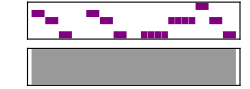

```mathematica
s[{
n[3],2,1,r,
n[3],2,1,r,
Subscript[{1,1,1,1}, 2],
Subscript[{2,2,2,2}, 2],
3,2,1,r
},5]//toObject//toSound
```

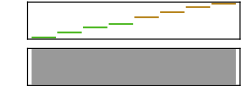

```mathematica
s[{
"Marimba"[s[{0,2,4,5}]],
"Xylophone"@{7,9,11,12}
}]//toObject//toSound
```

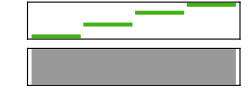

```mathematica
toObject["Marimba"[s[{0,2,4,5}]]]//toSound
```

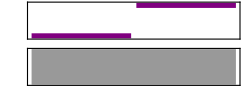

```mathematica
s[{
"Piano"[{0,4}]
}]//toObject//toSound
```

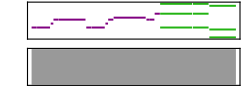

```mathematica
s[{
1,Subscript[1, 2.5],Subscript[2, 1/2],3,Subscript[3, 5],
1,Subscript[1, 2.5],Subscript[2, 1/2],3,Subscript[4, 6],
Subscript[3, 1/2],3,5,
Subscript["ElectricBass"[s[{
Subscript[p[{1,5,8}], 6],
Subscript[p[{1,5,8}], 3],
Subscript[p[{-2,0,7}], 5]}]], 14]
},13]//toObject//toSound
```

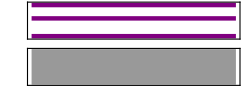

```mathematica
s[{
p[{1,3,5}]
}]//toObject//toSound
```

#### More Songs

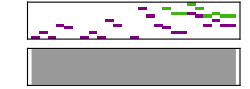

```mathematica
s[{
Subscript[n[-"so"], 2],n[-"so"],
Subscript[n[-"la"], 3],Subscript[n[-"so"], 3],
Subscript[8, 3],Subscript[7, 3],Subscript[r, 3],
Subscript[n[-"so"], 2],n[-"so"],
Subscript[n[-"la"], 3],Subscript[n[-"so"], 3],
Subscript[9, 3],Subscript[8, 3],Subscript[r, 3],
Subscript[n[-"so"], 2],n[-"so"],
Subscript[{12,10,8}, 9],p[{Subscript[{Subscript[7, 3],Subscript[6, 6]}, 9],"Marimba"@Subscript[{Subscript[12, 3],Subscript[11, 6]}, 9]},9],
p[{
{Subscript[11, 2],11,Subscript[10, 3],Subscript[8, 3],Subscript[9, 3],Subscript[8, 6]},
"Marimba"@{Subscript[13, 2],13,Subscript[12, 3],Subscript[10, 3],Subscript[11, 3],Subscript[10, 6]}},
18]
},9]//toObject//toSound
```